# MGDrivE: MCR Analysis

```mathematica
(*Set the path for the experiments*)
USER=3;
return=If[USER==1,SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR"],1];
return=If[USER==2,SetDirectory["/Volumes/Pusheen/xjego-khuq3/MCR"],1];
return=If[USER==3,SetDirectory["/Users/sanchez.hmsc/Desktop/MCR"],1];
If[return==1,Print["PATH ERROR"],Print["Path setup correctly"]];
(*Set a name for the outputs and define experiment's ranges*)
experimentName="MCR_AL_";
{releasesStart,releasesInterval,timeRange}={25,7,{1,365*3-1}};
(*Select the aggregation indices for genotypes*)
genotypesGroups={
{{2,5,5,6,7},"H"},
{{1,1,2,3,4},"W"},
{{3,6,8,8,9},"R"},
{{4,7,9,10,10},"B"}
};
(*Define genotypes colors*)
originalColorsValues={
{0,100,70,0},
{70,50,0,0},
{50,100,0,0},
{0,100,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
Transpose[{rgbColors,genotypesGroups[[All,2]]}]//Grid
```

Path setup correctly

RGBColor[1., 0., 0.30000000000000004] | H
RGBColor[0.30000000000000004, 0.5, 1.] | W
RGBColor[0.5, 0., 1.] | R
RGBColor[1., 0., 1.] | B

## 0) Functions

```mathematica
AggregateByGenotype[rawDataTotal_,genotypesGroups_]:=Module[{aggregatedData,outputTotals,totals,transposedTotals},
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
transposedTotals
]
GenerateMatrixPlotsNonNormalized[aggregatedGroupData_,timeRange_,maxesMax_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1/maxPopSize]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
GenerateStreamChart[counts_]:=BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
,GridLines->{Range[0,50000,100],Range[0,1.5*counts//Flatten//Max,100]}
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
GetMaxPopulation[aggregatedGroupData_,genotypesGroups_,timeRange_]:=Module[{i,maxes,genotypeA,genotypeAtemp,maxesMax},
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
maxesMax
]
GenerateMatrixPlotsSplits[matrixPlots_]:=GraphicsGrid[Prepend[
Transpose[{Show[#,FrameTicks->None]&/@matrixPlots}],
{Show[matrixPlots,FrameTicks->None]}
]]
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateMatrixPlots[aggregatedGroupData_,timeRange_,maxesMax_,rgbaColors_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
CalculateCounts[aggregatedGroupData_,genotypesGroups_]:=Module[{genotypeTemp,genotypeTotal},
Table[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}]
]
```

## 1) Single Experiment Dynamics

```mathematica
(*Homing rate, Female deposition amount, H-allele fitness, B-allele fitness*)
experimentString="E_090_075_002_010";
```

Load Data

```mathematica
experimentFolders=FileNames[experimentString,Directory[]]
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last)
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&
```

{/Users/sanchez.hmsc/Desktop/MCR/E_090_075_002_010}

{ⅇ,90,75,2,10}

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
WW | WH | WR | WB | HH | HR | HB | RR | RB | BB

Aggregate Data By Genotype

```mathematica
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups];
maxPopSize=aggregatedGroupData//Flatten//Max;
```

Export Color Palette

```mathematica
SwatchLegend[rgbColors,genotypesGroups[[All,2]]
,LabelStyle->30
,LegendMarkerSize->25
]
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Export["./images/"<>"00_ColorSwatch.png",%,ImageResolution->500];
```

Plot

### Normalized

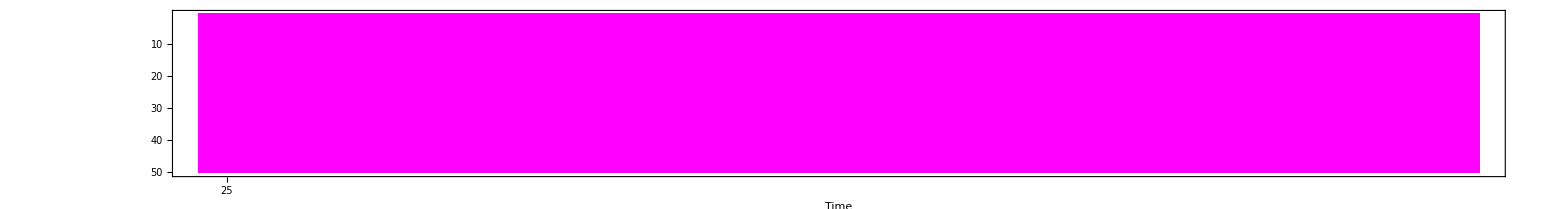

-Graphics-

./images/E_090_075_002_010-01.png

./images/E_090_075_002_010-02.png

```mathematica
maxesMax=GetMaxPopulation[aggregatedGroupData,genotypesGroups,timeRange];
matrixPlotsNM=GenerateMatrixPlots[aggregatedGroupData,timeRange,maxesMax];
matrixPlotsNN=GenerateMatrixPlotsNonNormalized[aggregatedGroupData,timeRange,maxesMax];
matrixPlotsCombinedNM=Show[matrixPlotsNM]
matrixPlotsCombinedNN=Show[matrixPlotsNN]
Export["./images/"<>experimentString<>"-01.png",matrixPlotsCombinedNM,ImageSize->5000]
Export["./images/"<>experimentString<>"-02.png",matrixPlotsCombinedNN,ImageSize->5000]
```

### Normalized Split

```mathematica
matrixPlotsSplit=GenerateMatrixPlotsSplits[matrixPlotsNN];
Export["./images/"<>experimentString<>"-03.png",matrixPlotsSplit,ImageSize->5000]
```

./images/E_090_075_002_010-03.png

### BarChart

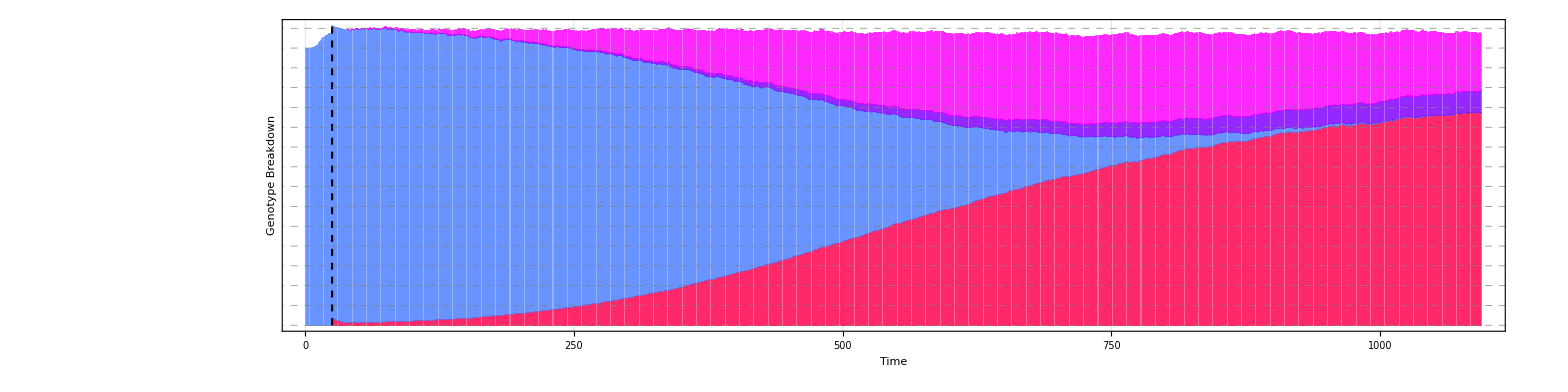

./images/E_090_075_002_010-04.png

```mathematica
counts=CalculateCounts[aggregatedGroupData,genotypesGroups];
streamChart=GenerateStreamChart[counts]
Export["./images/"<>experimentString<>"-04.png",streamChart,ImageSize->2500]
```

## 2) Single Experiment Batch

```mathematica
folderNames=Last/@(StringSplit[#,"/"]&/@FileNames["E_*",Directory[]]);
Print[ToString[Length[folderNames]]<>" folders loaded"];
```

2833 folders loaded

```mathematica
releaseTimes={releasesStart,(1*releasesInterval)+releasesStart};
(*Export plots loop*)
Table[
(*Process folders for analysis*)
experimentFolders=FileNames[folderNames[[i]],Directory[]];
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
(*Aggregate by genotype*)
aggregatedGroupData=AggregateByGenotype[rawDataTotal,genotypesGroups];
(*Plot 1*)
maxPopSize=aggregatedGroupData//Flatten//Max;
maxesMax=GetMaxPopulation[aggregatedGroupData,genotypesGroups,timeRange];
(*matrixPlotsNM=GenerateMatrixPlots[aggregatedGroupData,timeRange,maxesMax];*)
matrixPlotsNN=GenerateMatrixPlotsNonNormalized[aggregatedGroupData,timeRange,maxesMax];
(*Plot 2*)
matrixPlotsSplit=GenerateMatrixPlotsSplits[matrixPlotsNN];
(*Plot 3*)
counts=CalculateCounts[aggregatedGroupData,genotypesGroups];
streamChart=GenerateStreamChart[counts];
(*Export plots*)
fileName=StringSplit[cellFolder,"/"]//Last;
(*Export["./images/"<>fileName<>"-01.png",matrixPlotsCombinedNM,ImageSize->2500];*)
Export["./images/"<>fileName<>"-02.png",matrixPlotsCombinedNN,ImageSize->2500];
Export["./images/"<>fileName<>"-03.png",matrixPlotsSplit,ImageSize->2500];
Export["./images/"<>fileName<>"-04.png",streamChart,ImageSize->2000];
,{i,1,folderNames//Length}]
```

$Aborted

## 3) Factorial Grid

Load Data

```mathematica
(*:--------: User Input    :--------:*)
{experimentName,experimentFilter}={"MCR/2018_08_24_ANALYZED","E*"};
timeRange={1,365*10-1};
releasesStart=20;
genotypesGroups={
{{2,6,6,7,8,9},"H"},
{{1,1,2,3,4,5},"W"},
{{3,10,10,11,12},"R"},
{{4,8,11,13,13},"B"}
};
(*:--------: Get Folders   :--------:*)
directoryData=Directory[]<>"/"<>experimentName<>"/";
experimentFolders=FileNames[experimentFilter,directoryData];
Length[experimentFolders]
```

```mathematica
factorialData=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,geography,driveSystem,homing,resistant,broken}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM*","AF1*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
(*Aggregate by group*)
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
aggregatedGroupData=transposedTotals;
(*Mosquito counts*)
counts=ParallelTable[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}];
(*Mosquito Ratios*)
ratio=(#[[2]]/(#[[1]]+#[[2]])&/@{counts})[[1]];
ratioTime=Transpose[{Range[ratio//Length],counts[[1]],counts[[2]],counts[[3]],counts[[4]]}];
Flatten/@({ConstantArray[{homing,resistant,broken},ratio//Length],ratioTime}//Transpose)
,{i,1,experimentFolders//Length}];
flattenedData=Flatten[factorialData,1];
```

Plot Data

```mathematica
{day,{min,max}}={75,{.3,1}};
selectedDataSliceA=Cases[flattenedData,{hIn_,rIn_,bIn_,Round[day],hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,(wOut+rOut+bOut)/(hOut+wOut+rOut+bOut)}];
selectedDataSliceB=Cases[flattenedData,{hIn_,rIn_,bIn_,Round[day],hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,hOut/(hOut+wOut+rOut+bOut)}];
neutralPlot=ListDensityPlot3D[
selectedDataSliceA
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"DeepSeaColors",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
,PlotLabel->Style["Wild and Neutral Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
homingPlot=ListDensityPlot3D[
selectedDataSliceB
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"ValentineTones",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
,PlotLabel->Style["Homing Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
GraphicsGrid[{
{neutralPlot,homingPlot}
}
,ImageSize->2000
]
```

Animated Data

```mathematica
Table[
{min,max}={.3,1};
selectedDataSliceA=Cases[flattenedData,{hIn_,rIn_,bIn_,Round[day],hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,(wOut+rOut+bOut)/(hOut+wOut+rOut+bOut)}];
selectedDataSliceB=Cases[flattenedData,{hIn_,rIn_,bIn_,Round[day],hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,hOut/(hOut+wOut+rOut+bOut)}];
neutralPlot=ListDensityPlot3D[
selectedDataSliceA
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"DeepSeaColors",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
(*,PerformanceGoal->"Speed"*)
,PlotLabel->Style["Wild and Neutral Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
homingPlot=ListDensityPlot3D[
selectedDataSliceB
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"ValentineTones",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
(*,PerformanceGoal->"Speed"*)
,PlotLabel->Style["Homing Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
graphics=GraphicsGrid[{
{neutralPlot,homingPlot}
}
,ImageSize->3000
];
Export["./images/4D/"<>StringPadLeft[day//ToString,6,"0"]<>".png",graphics,ImageSize->3000];
ClearSystemCache[];
Clear[neutralPlot,homingPlot,graphics];
,{day,30,360}];
```

Animated Data (interpolated)

```mathematica
dayDatasetA=Cases[flattenedData,{hIn_,rIn_,bIn_,dayIn_,hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,dayIn,(wOut+rOut+bOut)/(hOut+wOut+rOut+bOut)}];
dayDatasetB=Cases[flattenedData,{hIn_,rIn_,bIn_,dayIn_,hOut_,wOut_,rOut_,bOut_}->{hIn/100,rIn/100,bIn/100,dayIn,hOut/(hOut+wOut+rOut+bOut)}];
predictorA=Predict[({#[[1]],#[[2]],#[[3]],#[[4]]}->#[[5]])&/@ dayDatasetA,Method->"LinearRegression"];
predictorB=Predict[({#[[1]],#[[2]],#[[3]],#[[4]]}->#[[5]])&/@ dayDatasetB,Method->"LinearRegression"];
```

```mathematica
Table[
{min,max}={.3,1};
tuples=Tuples[{Range[0,1,.25],Range[0,1,.25],Range[0,1,.25],ConstantArray[day,Range[0,1,.25]//Length]}];
selectedDataSliceA={#[[1]],#[[2]],#[[3]],predictorA[{#[[1]],#[[2]],#[[3]],#[[4]]}]}&/@tuples;
selectedDataSliceB={#[[1]],#[[2]],#[[3]],predictorB[{#[[1]],#[[2]],#[[3]],#[[4]]}]}&/@tuples;
neutralPlot=ListDensityPlot3D[
selectedDataSliceA
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"DeepSeaColors",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
,PlotLabel->Style["Wild and Neutral Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
homingPlot=ListDensityPlot3D[
selectedDataSliceB
,AxesLabel->(Style[#,30]&/@{"H","R","B"})
,AxesStyle->Directive[25]
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"ValentineTones",{max,min}}]
,ImageSize->750
,OpacityFunction->Interval[{min,max}]
,PlotLabel->Style["Homing Fraction\n",40]
,PlotRange->{{0,All},{0,All},{0,All}}
,ViewPoint->{-3,3,3}
];
graphics=GraphicsGrid[{
{neutralPlot,homingPlot}
}
,ImageSize->3000
];
Export["./images/4D/"<>StringPadLeft[Round[day*10]//ToString,6,"0"]<>".png",graphics,ImageSize->1000];
ClearSystemCache[];
Clear[neutralPlot,homingPlot,graphics];
,{day,40,70,.1}];
```

## 4) Experiment Factorial Data Analysis

Process Data

```mathematica
(*Experiment name = folder name*)
experimentName="2018_10_04_ANALYZED";
timeRange={1,365*10-1};
releasesStart=20;
directoryData=Directory[]<>"/"<>experimentName<>"/"
homingID="E_050";
folderNames=Last/@(StringSplit[#,"/"]&/@FileNames[homingID<>"*",directoryData]);
Length[folderNames]
```

/Users/sanchez.hmsc/Desktop/MCR/2018_10_04_ANALYZED/

405

```mathematica
rawDataFull=Table[
experimentString=folderNames[[i]];
experimentFolders=FileNames[experimentString,directoryData];
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
(**)
genotypesGroups={
{{2,5,5,6,7},"H"},
{{1,1,2,3,4},"W"},
{{3,6,8,8,9},"R"},
{{4,7,9,10,10},"B"}
};
(*Aggregate by group*)
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
aggregatedGroupData=transposedTotals;
(**)
counts=ParallelTable[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}];
(*Reshape*)
data=Flatten/@Transpose[Prepend[Prepend[counts,Range[counts[[1]]//Length]],ConstantArray[{homing,femaleDeposition,hCost,bCost},counts[[1]]//Length]]];
(**)
{
#[[1]]/100//N,
#[[2]]/100//N,
#[[3]]/100//N,
#[[4]]/100//N,
#[[5]]//N,
#[[6]]//N,
#[[7]]//N,
#[[8]]//N,
#[[9]]//N
}&/@data
,{i,1,Length[folderNames]}];
```

```mathematica
Export[
homingID<>"_MCR_Ext.csv",
Prepend[Flatten[rawDataFull,1],{"Homing","FemaleDeposition","HFitness","BFitness","Day","H","W","R","B"}]
]
```

E_050_MCR_Ext.csv

Track Buggy Files

## Find Folder with Error

```mathematica
rawDataFull=Table[
experimentString=folderNames[[i]];
experimentFolders=FileNames[experimentString,directoryData];
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
Print[{cellFolder,Map[Length,rawData,Infinity]}];
,{i,1,Length[folderNames]}];
```

## Find File with Error

```mathematica
experimentString="E_085_075_004_025";
experimentFolders=FileNames[experimentString,directoryData];
cellFolder=experimentFolders[[1]];
sweepID={null,homing,femaleDeposition,hCost,bCost}=ToExpression/@(StringSplit[StringSplit[cellFolder,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_Mean*","AF1_Mean*"};
rawData={rawDataMale,rawDataFemale}=ParallelMap[
Import[#][[2;;All,2;;All]]&
,#]&/@filenames;
Transpose/@({filenames,Map[Length,rawData,{2}]}//Transpose)
```

{{{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0000.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0001.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0002.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0003.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0004.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0005.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0006.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0007.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0008.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0009.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0010.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0011.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0012.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0013.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0014.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0015.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0016.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0017.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0018.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0019.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0020.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0021.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0022.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0023.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0024.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0025.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0026.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0027.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0028.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0029.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0030.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0031.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0032.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0033.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0034.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0035.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0036.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0037.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0038.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0039.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0040.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0041.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0042.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0043.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0044.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0045.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0046.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0047.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0048.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/ADM_Mean_Patch0049.csv,3649}},{{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0000.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0001.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0002.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0003.csv,3197},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0004.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0005.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0006.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0007.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0008.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0009.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0010.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0011.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0012.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0013.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0014.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0015.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0016.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0017.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0018.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0019.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0020.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0021.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0022.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0023.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0024.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0025.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0026.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0027.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0028.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0029.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0030.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0031.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0032.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0033.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0034.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0035.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0036.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0037.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0038.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0039.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0040.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0041.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0042.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0043.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0044.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0045.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0046.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0047.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0048.csv,3649},{/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR/Invasiveness_Autosomal_090418/2018_09_04_ANALYZED/E_085_075_004_025/AF1_Mean_Patch0049.csv,3649}}}

Analyze Data

```mathematica
{homingID,day}={"E_095",999};
(*Experiment name = folder name*)
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>homingID<>"_MCR_Ext.csv"][[2;;All]];
maxMosquito=Flatten[sampledData[[All,4;;All]]]//Max;
```

```mathematica
homing=StringSplit[homingID,"_"]//Last//ToExpression;
samplePoint=Cases[sampledData,{sampledData[[2]][[1]],fd_,hc_,bc_,sampledData[[All,5]][[day]],h_,w_,r_,b_}->{fd/100,hc/100,bc/100,h,w,r,b}];
```

```mathematica
sampledLayerH={#[[1]],#[[2]],#[[3]],#[[4]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerW={#[[1]],#[[2]],#[[3]],#[[5]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerR={#[[1]],#[[2]],#[[3]],#[[6]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerB={#[[1]],#[[2]],#[[3]],#[[7]]/(maxMosquito)}&/@samplePoint//N;

function1[x_]:=Blend[{Darker[White,0],Darker[Blue,.3],Darker[White,.0]},x]
function2[x_]:=Blend[{Darker[White,0],Darker[Red,.3],Darker[White,.0]},x]
function3[x_]:=Blend[{Darker[White,0],Darker[Purple,.3],Darker[White,.0]},x]
function4[x_]:=Blend[{Darker[White,0],Darker[Magenta,.3],Darker[White,.0]},x]
```

```mathematica
plot=ListDensityPlot3D[#[[2]]
,AxesLabel->(Style[#,35]&/@{"F","H","B"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[Thick]
,ColorFunction->#[[3]]
,ColorFunctionScaling->True
,FaceGrids->{{0,-1,0},{0,0,-1},{1,0,0}}
,FaceGridsStyle->Directive[Opacity[.2],Thick]
,ImageSize->750
,PlotLabel->Style[#[[1]],75]
,OpacityFunction->Interval[{.3,1}]
,Ticks->Automatic
,TicksStyle->25
,ViewPoint->{-1.5,1.5,1.5}
]&/@Transpose[{{"W","H","R","B"},{sampledLayerW,sampledLayerH,sampledLayerR,sampledLayerB},{function1,function2,function3,function4}}];
grid=GraphicsGrid[{{plot[[1]],plot[[2]]},{plot[[3]],plot[[4]]}},ImageSize->2000];
Export["./images/AutosomalAnimation/"<>homingID<>"/"<>StringPadLeft[ToString[day],6,"0"]<>".png",grid,ImageSize->2000]
```

./images/AutosomalAnimation/E_095/000999.png

Animation

```mathematica
directoryData
```

/Volumes/Pusheen/xjego-khuq3/MCR/ProcessedData/Autosomal/

```mathematica
{homingID}={"E_099"};
(*Experiment name = folder name*)
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>homingID<>"_MCR_Ext.csv"][[2;;All]];
maxMosquito=Flatten[sampledData[[All,4;;All]]]//Max;
```

```mathematica
function1[x_]:=Blend[{Darker[White,0],Darker[Blue,.3],Darker[White,0]},x]
function2[x_]:=Blend[{Darker[White,0],Darker[Red,.3],Darker[White,0]},x]
function3[x_]:=Blend[{Darker[White,0],Darker[Purple,.3],Darker[White,0]},x]
function4[x_]:=Blend[{Darker[White,0],Darker[Magenta,.3],Darker[White,0]},x]
```

```mathematica
Table[
samplePoint=Cases[sampledData,{sampledData[[2]][[1]],fd_,hc_,bc_,sampledData[[All,5]][[day]],h_,w_,r_,b_}->{fd/100,hc/100,bc/100,h,w,r,b}];
sampledLayerH={#[[1]],#[[2]],#[[3]],#[[4]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerW={#[[1]],#[[2]],#[[3]],#[[5]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerR={#[[1]],#[[2]],#[[3]],#[[6]]/(maxMosquito)}&/@samplePoint//N;
sampledLayerB={#[[1]],#[[2]],#[[3]],#[[7]]/(maxMosquito)}&/@samplePoint//N;
plot=ListDensityPlot3D[#[[2]]
,AxesLabel->(Style[#,40]&/@{"F","H","B"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[Thick]
,ColorFunction->#[[3]]
,ColorFunctionScaling->True
,FaceGrids->{{0,-1,0},{0,0,-1},{1,0,0}}
,FaceGridsStyle->Directive[Opacity[.2],Thick]
,ImageSize->750
,PlotLabel->Style[#[[1]],80]
,OpacityFunction->Interval[{.5,1}]
,Ticks->Automatic
,TicksStyle->30
,ViewPoint->{-1.5,1.5,1.5}
]&/@Transpose[{{"W","H","R","B"},{sampledLayerW,sampledLayerH,sampledLayerR,sampledLayerB},{function1,function2,function3,function4}}];
grid=GraphicsGrid[{{plot[[1]],plot[[2]]},{plot[[3]],plot[[4]]}},ImageSize->2000];
Export["./images/AutosomalAnimation/"<>homingID<>"/"<>StringPadLeft[ToString[day],6,"0"]<>".png",grid,ImageSize->2000]
,{day,timeRange[[1]],timeRange[[2]]}];
```

$Aborted

## 5) Second Pass at Factorial Data Analysis

```mathematica
USER=2;
If[USER==1,SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR"],0];
(*If[USER==2,SetDirectory["/Volumes/Pusheen/xjego-khuq3/MCR"],0];*)
If[USER==2,SetDirectory["/Users/sanchez.hmsc/Desktop/MCR"],0];
```

Day Filtering

```mathematica
day=999;
(**)
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>#<>"processedData.csv"][[2;;All]]&/@{"E_065","E_070","E_075","E_080","E_085","E_090","E_095","E_099"};
```

```mathematica
flattenedData=Flatten[sampledData,1];
maxPop=Max[flattenedData[[All,6;;9]]];
levels=DeleteDuplicates/@(flattenedData[[All,1;;4]]//Transpose);
days=flattenedData[[All,5]]//DeleteDuplicates;
```

```mathematica
filtered=Cases[flattenedData,{homingRate_,fd_,hc_,bc_,days[[day]],h_,w_,r_,b_}->{homingRate,fd/100,hc/100,bc/100,h/maxPop,w/maxPop,r/maxPop,b/maxPop}];
Export[
"./ProcessedData/Autosomal/Day"<>StringPadLeft[ToString[day],4,"0"]<>".csv",
Prepend[filtered,{"Homing","FemaleDeposition","HFitness","BFitness","H","W","R","B"}]
]
```

./ProcessedData/Autosomal/Day0999.csv

Ratio Filtering

```mathematica
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>#<>"processedData.csv"][[2;;All]]&/@{"E_065","E_070","E_075","E_080","E_085","E_090","E_095","E_099"};
```

```mathematica
flattenedData=Flatten[sampledData,1];
maxPop=Max[flattenedData[[All,6;;9]]];
levels=DeleteDuplicates/@(flattenedData[[All,1;;4]]//Transpose);
days=flattenedData[[All,5]]//DeleteDuplicates;
```

```mathematica
Table[
{day,wThreshold}={999,i};
rescaled={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]/maxPop,#[[7]]/maxPop,#[[8]]/maxPop,#[[9]]/maxPop}&/@flattenedData;
filtered=Cases[rescaled,({homingRate_,fd_,hc_,bc_,days[[day]],h_,w_,r_,b_}/;w>wThreshold)->{homingRate,fd/100,hc/100,bc/100,h,w,r,b}];
Export[
"./ProcessedData/Autosomal/Day"<>StringPadLeft[ToString[day],4,"0"]<>"_"<>StringPadLeft[ToString[wThreshold*100//Round],3,"0"]<>".csv",
Prepend[filtered,{"Homing","FemaleDeposition","HFitness","BFitness","H","W","R","B"}]
]
,{i,0,.5,.05}]
```

{./ProcessedData/Autosomal/Day0999_000.csv,./ProcessedData/Autosomal/Day0999_005.csv,./ProcessedData/Autosomal/Day0999_010.csv,./ProcessedData/Autosomal/Day0999_015.csv,./ProcessedData/Autosomal/Day0999_020.csv,./ProcessedData/Autosomal/Day0999_025.csv,./ProcessedData/Autosomal/Day0999_030.csv,./ProcessedData/Autosomal/Day0999_035.csv,./ProcessedData/Autosomal/Day0999_040.csv,./ProcessedData/Autosomal/Day0999_045.csv,./ProcessedData/Autosomal/Day0999_050.csv}

Ratio Filtering Analysis

```mathematica
experimentName="ProcessedData/Autosomal";
directoryData=Directory[]<>"/"<>experimentName<>"/";
sampledData=Import[directoryData<>#<>"processedData.csv"][[2;;All]]&/@{"E_065","E_070","E_075","E_080","E_085","E_090","E_095","E_099"};
```

```mathematica
flattenedData=Flatten[sampledData,1];
maxPop=Max[flattenedData[[All,6;;9]]];
levels=DeleteDuplicates/@(flattenedData[[All,1;;4]]//Transpose);
days=flattenedData[[All,5]]//DeleteDuplicates;
```

```mathematica
tables=Table[
{day,wThreshold}={999,.2};
rescaled={#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]/maxPop,#[[7]]/maxPop,#[[8]]/maxPop,#[[9]]/maxPop}&/@flattenedData;
filtered=Cases[rescaled,({homingRate_,fd_,hc_,bc_,days[[day]],h_,w_,r_,b_}/;w>wThreshold)->{homingRate,fd/100,hc/100,bc/100,h,w,r,b}];
{#[[1]],#[[2]],#[[3]],#[[4]],#[[6]]}&/@filtered//Grid[Prepend[#,{"Homing","FDeposition","Hfit","Bfit","W"}]]&
,{i,0,.4,.05}];
```

```mathematica
tables//Grid[{#},Frame->All]&
```

Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468 | Homing | FDeposition | Hfit | Bfit | W
0.65 | 0.0075 | 0.0004 | 0.0035 | 0.208538
0.65 | 0.0075 | 0.0006 | 0.002 | 0.225223
0.65 | 0.0075 | 0.0006 | 0.0035 | 0.24302
0.65 | 0.0075 | 0.0006 | 0.004 | 0.281246
0.65 | 0.0075 | 0.0008 | 0.0005 | 0.25586
0.65 | 0.0075 | 0.0008 | 0.001 | 0.232469
0.65 | 0.0075 | 0.0008 | 0.002 | 0.244426
0.65 | 0.0075 | 0.0008 | 0.0025 | 0.315024
0.65 | 0.0075 | 0.0008 | 0.003 | 0.261912
0.65 | 0.0075 | 0.0008 | 0.0035 | 0.376429
0.65 | 0.0075 | 0.0008 | 0.004 | 0.338186
0.65 | 0.0075 | 0.001 | 0.0005 | 0.247322
0.65 | 0.0075 | 0.001 | 0.001 | 0.24688
0.65 | 0.0075 | 0.001 | 0.0015 | 0.376135
0.65 | 0.0075 | 0.001 | 0.002 | 0.27948
0.65 | 0.0075 | 0.001 | 0.0025 | 0.366697
0.65 | 0.0075 | 0.001 | 0.003 | 0.367286
0.65 | 0.0075 | 0.001 | 0.0035 | 0.320864
0.65 | 0.0075 | 0.001 | 0.004 | 0.443641
0.7 | 0.0075 | 0.0006 | 0.003 | 0.20844
0.7 | 0.0075 | 0.0006 | 0.004 | 0.201178
0.7 | 0.0075 | 0.0008 | 0.0025 | 0.206641
0.7 | 0.0075 | 0.0008 | 0.003 | 0.25604
0.7 | 0.0075 | 0.0008 | 0.0035 | 0.225615
0.7 | 0.0075 | 0.0008 | 0.004 | 0.216815
0.7 | 0.0075 | 0.001 | 0.0005 | 0.209487
0.7 | 0.0075 | 0.001 | 0.001 | 0.247256
0.7 | 0.0075 | 0.001 | 0.0015 | 0.309414
0.7 | 0.0075 | 0.001 | 0.002 | 0.24513
0.7 | 0.0075 | 0.001 | 0.0025 | 0.319342
0.7 | 0.0075 | 0.001 | 0.003 | 0.262812
0.7 | 0.0075 | 0.001 | 0.0035 | 0.381075
0.7 | 0.0075 | 0.001 | 0.004 | 0.36668
0.75 | 0.0075 | 0.0008 | 0.0025 | 0.221968
0.75 | 0.0075 | 0.0008 | 0.004 | 0.279676
0.75 | 0.0075 | 0.001 | 0.002 | 0.228085
0.75 | 0.0075 | 0.001 | 0.0025 | 0.229361
0.75 | 0.0075 | 0.001 | 0.003 | 0.267981
0.75 | 0.0075 | 0.001 | 0.0035 | 0.338971
0.75 | 0.0075 | 0.001 | 0.004 | 0.325411
0.8 | 0.0075 | 0.0008 | 0.004 | 0.229803
0.8 | 0.0075 | 0.001 | 0.003 | 0.213364
0.8 | 0.0075 | 0.001 | 0.0035 | 0.215556
0.8 | 0.0075 | 0.001 | 0.004 | 0.254977
0.85 | 0.0075 | 0.001 | 0.0035 | 0.203468